```mathematica
cantor1[{p_, q_}] := 1/3{{3p, 2p + q},{p + 2q, 3q}}
c0 = {{SetPrecision[0, MachinePrecision],SetPrecision[1, MachinePrecision]}};
```

```mathematica
cantor2[list_] := Flatten[Map[cantor1, list], 1]
```

```mathematica
cantor3[n_, list_] := Nest[cantor2, list, n]
```

```mathematica
make2d[{p_, q_}] := {{p, 0}, {q, 0}}
```

```mathematica
cantor31[n_, list_] := Map[make2d, cantor3[n, list]]
```

```mathematica
cantor4[n_, list_] := Graphics[{Black,Line[cantor31[n, list]]},AspectRatio->0.02,ImageSize->900]
```

```mathematica
cantor4[7, c0]
```

```mathematica
cantor5[n_, list_] := GraphicsColumn[Table[cantor4[m, list], {m, 0,n}]]
```

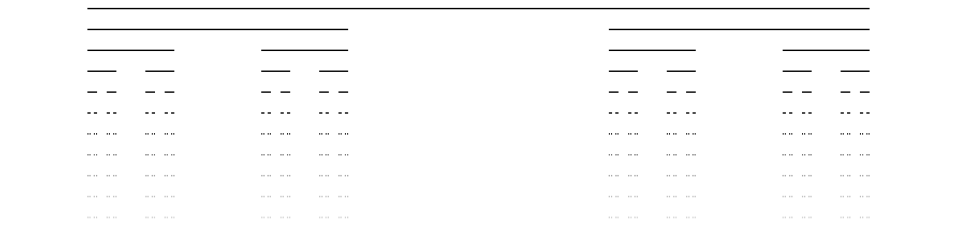

```mathematica
cantor5[10, c0]
```